# npn-Transistor

## Funktionen

### Includes

```mathematica
Needs["ErrorBarPlots`"]
```

### Fehlerfunktion(Größtfehler) ∑(|df/dx_i|Δx_i)

```mathematica
GError[a_,b_,c_]:= (Total[Map[Abs,MapThread[D,{Table[a,{i,1,Length[b]}],b}]]*c]);
```

### Gaussfunktion

```mathematica
Gauss[a_]:={Mean[a],StandardDeviation[a]/(√Length[a])}
```

### Basics

```mathematica
fAdd[va_,dva_,vb_,dvb_]:=Module[{f,fe,a,b,da,db},
f=a+b;
fe=GError[f,{a,b},{da,db}];
{f,fe}/.{a->va,b->vb,da->dva,db->dvb}]
```

```mathematica
Fdiv[a1_,da1_,b1_,db1_]:= Module[{f,fe,a,b,da,db},
f=a/b;
fe = GError[f,{a,b},{da,db}];
{f,fe}/.{a->a1,da->da1,b-> b1,db->db1}]
```

```mathematica
Fmult[γ_,dγ_,δ_,dδ_]:= Module[{f,fe,a,b,da,db},
f=a*b;
fe = GError[f,{a,b},{da,db}];
{f,fe}/.{a->γ,da->dγ,b-> δ,db->dδ}]
```

```mathematica
Ff[a1_,da1_,b1_,db1_,c1_,dc1_]:= Module[{f,fe,a,b,c,da,db,dc},
f=a*b/c;
fe = GError[f,{a,b,c},{da,db,dc}];
{f,fe}/.{a->a1,da->da1,b-> b1,db->db1,c->c1,dc->dc1}]
```

## Vorlage

## 1.) Vierquadrantenkennlinienfeld eines npn-Transistors

```mathematica
i20 =20 *10^-6;
i50 = 50 *10^-6;
i100=100 *10^-6;
```

```mathematica
ti20={{"U_CE", "I_C", "U_BE"}, {□, □, □}, {□, □, □}, {□, □, □}, {□, □, □}, {□, □, □}, {□, □, □}, {□, □, □}, {□, □, □}, {□, □, □}, {□, □, □}};
ti50={{"U_CE", "I_C", "U_BE"}, {□, □, □}, {□, □, □}, {□, □, □}, {□, □, □}, {□, □, □}, {□, □, □}, {□, □, □}, {□, □, □}, {□, □, □}, {□, □, □}};
ti100={{"U_CE", "I_C", "U_BE"}, {□, □, □}, {□, □, □}, {□, □, □}, {□, □, □}, {□, □, □}, {□, □, □}, {□, □, □}, {□, □, □}, {□, □, □}, {□, □, □}};
```

```mathematica
dti20= Table[{ti20[[x,1]]*0.01+0.001,ti20[[x,2]]*0.015+0.01},{x,2,Length[ti20]}];
dti50= Table[{ti50[[x,1]]*0.01+0.001,ti50[[x,2]]*0.015+0.01},{x,2,Length[ti50]}];
dti100= Table[{ti100[[x,1]]*0.01+0.001,ti100[[x,2]]*0.015+0.01},{x,2,Length[ti100]}];
```

```mathematica
(*p1 = Table[{{dt[[x,1]],dt[[x,2]]},ErrorBar[ddt[[x,1]],ddt[[x,2]]]},{x,1,Length[dt]}]
ErrorListPlot[p1,Joined-> True,AxesOrigin-> {0,0},AxesLabel-> {"U/V","I/mA"},PlotRange->{{0,0.8},{0,140}}]*)
```

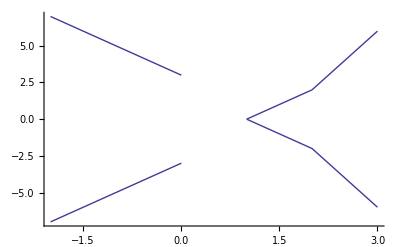

```mathematica
Show[ListPlot[{{1,0},{2,2},{3,6}},Joined->True],ListPlot[{{0,3},{-1,5},{-2,7}},Joined->True],ListPlot[{{0,-3},{-1,-5},{-2,-7}},Joined->True],ListPlot[{{1,0},{2,-2},{3,-6}},Joined->True]]
```

## 2.) Transistor-Verstärkerschaltung

```mathematica
ic = {{5, 1}}*10^-3;
```